```mathematica
(*THIS NOTEBOOK PROVIDES A SET OF TESTS FOR THE BELIEFPROPAGATION.WL PACKAGE ALGORITHMS*)
(*Disclaimer: This software is provided without any warranty express or implied Stuart Nettleton 2020*)
(*Requires Wolfram Mathematica 12.1.0.0 or higher*)
(*All code files and executable documents are with the license GPL 3.0.For details see http://www.gnu.org/licenses/.*)
(*All documents are with the license Creative Commons Attribution 4.0 International (CC BY 4.0).For details see https://creativecommons.org
licenses/by/4.0/.*)
(*Based on a scheme provided by Daphne Koller in the Stanford University Subject Probabilistic Graphical Models, Copyright (C) Daphne Koller, Stanford University, 2012*)
ClearAll["Global`*"];
SetDirectory["/home/stuart/Documents/mathematica/pgms"];
<<beliefPropagation.wl
directory="beliefPropagationTestData/";
Print[Style["EXACT BELIEF PROPAGATION",{Larger,Red,Bold}]];
indexToAssignmentInput=Get[directory<>"indexToAssignmentInput.txt"];
indexToAssignmentOutput=Get[directory<>"indexToAssignmentOutput.txt"];
Print["indexToAssignment test: ",indexToAssignment@@indexToAssignmentInput==indexToAssignmentOutput]
assignmentToIndexInput=Get[directory<>"assignmentToIndexInput.txt"];
assignmentToIndexOutput=Get[directory<>"assignmentToIndexOutput.txt"];
Print["assignmentToIndex test: ",assignmentToIndex@@#&/@assignmentToIndexInput==assignmentToIndexOutput]
factorProductOrSumInput1=Get[directory<>"factorProductOrSumInput1.txt"];
factorProductOrSumOutput1=Get[directory<>"factorProductOrSumOutput1.txt"];
Print["Factor Product Sum Test 1 ... ",factorProductOrSum[##,False]&@@factorProductOrSumInput1==factorProductOrSumOutput1]
factorProductOrSumInput2=Get[directory<>"factorProductOrSumInput2.txt"];
factorProductOrSumOutput2=Get[directory<>"factorProductOrSumOutput2.txt"];
Print["Factor Product Sum Test 2 ... ",factorProductOrSum[##,False]&@@factorProductOrSumInput2[[;;2]]==factorProductOrSumOutput2]
factorMarginalizationInput1=Get[directory<>"factorMarginalizationInput1.txt"];
factorMarginalizationOutput1=Get[directory<>"factorMarginalizationOutput1.txt"];
Print["Factor Marginalization Sum Test 1 ... ",factorMarginalization[##,False]&@@factorMarginalizationInput1==factorMarginalizationOutput1]
factorMarginalizationInput2=Get[directory<>"factorMarginalizationInput2.txt"];
factorMarginalizationOutput2=Get[directory<>"factorMarginalizationOutput2.txt"];
Print["Factor Marginalization Max Test 2... ",factorMarginalization[##,True]&@@factorMarginalizationInput2==factorMarginalizationOutput2]
observeEvidenceInput=Get[directory<>"observeEvidenceInput.txt"];
observeEvidenceOutput=Get[directory<>"observeEvidenceOutput.txt"];
Print["Observe Evidence Test ... ",observeEvidence[##]&@@observeEvidenceInput==observeEvidenceOutput]
computeJointDistributionInput=Get[directory<>"computeJointDistributionInput.txt"];
computeJointDistributionOutput=Get[directory<>"computeJointDistributionOutput.txt"];
Print["Joint Distribution Test ... ",computeJointDistribution[computeJointDistributionInput]==computeJointDistributionOutput]
computeMarginalInput=Get[directory<>"computeMarginalInput.txt"];
computeMarginalOutput=Get[directory<>"computeMarginalOutput.txt"];
Print["Compute Marginal Test ... ",computeMarginal@@computeMarginalInput==computeMarginalOutput]
inputInitialPotentialsInput=Get[directory<>"inputInitialPotentialsInput.txt"];
inputInitialPotentialsResult=Get[directory<>"inputInitialPotentialsResult.txt"];
cip=computeInitialPotentials[inputInitialPotentialsInput];
Print["computeInitialPotentials test: ",cip==inputInitialPotentialsResult]
ptInput=Get[directory<>"ptInput.txt"];
pt=pruneTree[ptInput];
Print["Prune Tree test: ",pt==First@inputInitialPotentialsResult]
createCliqueTreeInput=Last@inputInitialPotentialsInput;
createCliqueTreeOutputA=inputInitialPotentialsResult;
createCliqueTreeOutputB=Get[directory<>"createCliqueTreeOutputB.txt"];
cct=createCliqueTree[createCliqueTreeInput,{}];
Print["Create Clique Tree test: factors : ",Last@cct==Last@createCliqueTreeOutputA," ... edges: ",First@cct==First@createCliqueTreeOutputB]
gncInput1=Get[directory<>"gncInput1.txt"];
gncInput2=Get[directory<>"gncInput2.txt"];
gnc=getNextCliques[gncInput1,gncInput2];
Print["Get Next Cliques test: ",gnc=={9,2}];
sumprodInput=Get[directory<>"sumprodInput.txt"];
sumprodResult=Get[directory<>"sumprodResult.txt"];
sumprodResult=Join[{First@sumprodResult},{Join[sumprodResult[[-1,All,;;2]],N@{#}&/@Round[sumprodResult[[-1,All,-1]],10^-6],2]}];
ctc=cliqueTreeCalibrate[sumprodInput,False];
ctc=Join[{First@ctc},{Join[ctc[[-1,All,;;2]],N@{#}&/@Round[ctc[[-1,All,-1]],10^-6],2]}];
Print["Clique Tree Calibrate SumProduct test factors: ",Last@ctc==Last@sumprodResult," ... edges: ",First@ctc==First@sumprodResult]
cemspFactorsInput=Get[directory<>"cemspFactorsInput.txt"];
cemspResult=Get[directory<>"cemspResult.txt"];
Print["ComputeExactMarginalsBP SumProduct test: ",computeExactMarginalsBP[cemspFactorsInput,{},False]==cemspResult]
computeExactMarginalsBPocrInput=Get[directory<>"computeExactMarginalsBPocrInput.txt"];
computeExactMarginalsBPocrOutput=Get[directory<>"computeExactMarginalsBPocrOutput.txt"];
Print["ComputeExactMarginalsBP MaxProduct test: ",computeExactMarginalsBP[computeExactMarginalsBPocrInput,{},True]==computeExactMarginalsBPocrOutput]
maxDecodedInput=Get[directory<>"maxDecodedInput.txt"];
maxDecodedOutput=Get[directory<>"maxDecodedOutput.txt"];
md=maxDecoded[maxDecodedInput];
Print["Max Decoded test: ",First@md==maxDecodedOutput," ... alphabet mapped ... ",Last@md]
Print[Style["LOOPY BELIEF PROPAGATION",{Larger,Red,Bold}]];
naiveGetNextClustersInput1=Get[directory<>"naiveGetNextClustersInput1.txt"];
naiveGetNextClustersInput2=Get[directory<>"naiveGetNextClustersInput2.txt"];
naiveGetNextClustersOutput=Get[directory<>"naiveGetNextClustersOutput.txt"];
Print["naiveGetNextClusters test: ",naiveGetNextClusters[naiveGetNextClustersInput1,#]&/@naiveGetNextClustersInput2==naiveGetNextClustersOutput]
createClusterGraphInput=Get[directory<>"createClusterGraphInput.txt"];
createClusterGraphOuput=Get[directory<>"createClusterGraphOuput.txt"];
ccg=createClusterGraph[createClusterGraphInput,{}];
Print["createClusterGraph test: ",First@ccg==createClusterGraphOuput]
checkConvergenceInput1=Get[directory<>"checkConvergenceInput1.txt"];
checkConvergenceInput2=Get[directory<>"checkConvergenceInput2.txt"];
cc=MapThread[checkConvergence,{checkConvergenceInput1,checkConvergenceInput2}];
Print["checkConvergence test: ",cc=={True,False}]
clusterGraphCalibrateInput=Get[directory<>"clusterGraphCalibrateInput.txt"];
clusterGraphCalibrateOutputFactors=Get[directory<>"clusterGraphCalibrateOutputFactors.txt"];
clusterGraphCalibrateOutputMessages=Get[directory<>"clusterGraphCalibrateOutputMessages.txt"];
cgc=clusterGraphCalibrate[clusterGraphCalibrateInput,False,False];
Print["clusterGraphCalibrate factors test: ",First@cgc==clusterGraphCalibrateOutputFactors," ... messages test: ",Last@cgc==clusterGraphCalibrateOutputMessages];
computeApproxMarginalsBPfactors=Get[directory<>"computeApproxMarginalsBPfactors.txt"];
computeApproxMarginalsBPoutput=Get[directory<>"computeApproxMarginalsBPoutput.txt"];
cam=computeApproxMarginalsBP[computeApproxMarginalsBPfactors,{},False,False];
Print["computeApproxMarginalsBP test: ",cam==computeApproxMarginalsBPoutput]
```

Attributes::locked: Symbol beliefPropagation is locked.

EXACT BELIEF PROPAGATION

indexToAssignment test: True

assignmentToIndex test: True

Factor Product Sum Test 1 ... True

Factor Product Sum Test 2 ... True

Factor Marginalization Sum Test 1 ... True

Factor Marginalization Max Test 2... True

Observe Evidence Test ... True

Joint Distribution Test ... True

Compute Marginal Test ... True

computeInitialPotentials test: True

Prune Tree test: True

Create Clique Tree test: factors : True ... edges: True

Get Next Cliques test: True

Clique Tree Calibrate SumProduct test factors: True ... edges: True

ComputeExactMarginalsBP SumProduct test: True

ComputeExactMarginalsBP MaxProduct test: True

Max Decoded test: True ... alphabet mapped ... topoost

LOOPY BELIEF PROPAGATION

naiveGetNextClusters test: True

createClusterGraph test: True

checkConvergence test: True

LBP Messages Passed: 96

Total number of messages passed: 96 in 0.094738 seconds

clusterGraphCalibrate factors test: True ... messages test: True

LBP Messages Passed: 96

Total number of messages passed: 96 in 0.088764 seconds

computeApproxMarginalsBP test: True

```mathematica
(*KEEP THESE TESTS SEPARATE AS TAKES 1 MIN & SO LONG TIME FOR QUICK INITIAL TESTS*)
sixPersonFactors=Get[directory<>"sixPersonFactors_Input.txt"];
Print["ComputeExactMarginalsBP sixPersonFactors Sum test: ",First@computeExactMarginalsBP[sixPersonFactors,{},False]==computeMarginal[{1},sixPersonFactors,{}]]
Print["ComputeExactMarginalsBP sixPersonFactors Sum test with evidence: ",computeExactMarginalsBP[sixPersonFactors,{{1,1}},False][[5]]==computeMarginal[{5},sixPersonFactors,{{1,1}}]]
maxprodInput=Get[directory<>"cliqueTreeCalibrate_maxprodInput.txt"];
ctc=cliqueTreeCalibrate[maxprodInput,True];
maxprodResult=Get[directory<>"cliqueTreeCalibrate_maxprodResult.txt"];
Print["Clique Tree Calibrate MaxProduct test factors: ",!Or@@(#>10^-3&/@Flatten@(Last/@(Abs@Quiet[Last@ctc-Last@maxprodResult]/.{Indeterminate->0})))," ... edges: ",First@ctc==First@maxprodResult]
```

ComputeExactMarginalsBP sixPersonFactors Sum test: True

ComputeExactMarginalsBP sixPersonFactors Sum test with evidence: True

Clique Tree Calibrate MaxProduct test factors: True ... edges: True

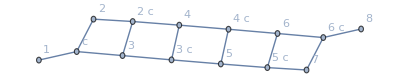

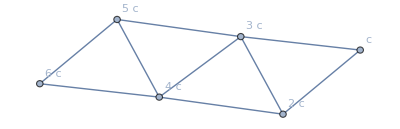

Clique Tree Calibrate MaxProduct test factors: True

```mathematica
(*KEEP THIS TEST SEPARATE AS TAKES 20 MINS TO RUN*)
ocr=Get[directory<>"computeExactMarginalsBP_ocr.txt"];
maxMarginals=computeExactMarginalsBP[ocr,{},True,"Kruskal",True];
MAPAssignment=maxDecoded[maxMarginals];
Print["Clique Tree Calibrate MaxProduct test factors: ",Last@MAPAssignment=="mornings"]
```